## Implémentation des DLL C++

## Import de la DLL

```mathematica
Clear[pathToDll]
```

```mathematica
Needs["NETLink`"];
```

```mathematica
InstallNET[];
```

```mathematica
(*pathToDll="C:\\Users\\Clem\\Documents\\ESGI\\projet_annuel_ibd3a\\C++_lib\\Dll-Machine-Learning\\x64\\Debug\\Dll-Machine-Learning.dll";*)pathToDll="D:\\git\\projet_annuel_ibd3a\\C++_lib\\Dll-Machine-Learning\\x64\\Debug\\Dll-Machine-Learning.dll";
```

```mathematica
return42ExternFunc=DefineDLLFunction["return42",pathToDll,"int",{}];
```

```mathematica
return42ExternFunc[]
```

42

## Définitions Méthodes C++

```mathematica
Clear[createLinearModelClassif, linearFitClassificationRosenblatt, linearClassify, linearCreateAndFitRegression, linearPredict, createMlp, classify, fitClassification, predict, eraseMlp, getOutputsforRegression];
```

Perceptron Linéaire simple

## Création modèle

```mathematica
createLinearModelClassif = DefineDLLFunction["createLinearModelClassif", pathToDll, "System.IntPtr", {"int", "int"}];
```

## Classification Linéaire Rosenblatt

```mathematica
linearFitClassificationRosenblatt = DefineDLLFunction["linearFitClassificationRosenblatt", pathToDll, "int", {"System.IntPtr", "double[]", "int", "double[]", "int", "double"}];
```

```mathematica
linearClassify =  DefineDLLFunction["linearClassify", pathToDll, "double", {"System.IntPtr", "double[]", "int", "double[]", "int"}];
```

## Régression linéaire

```mathematica
linearCreateAndFitRegression = DefineDLLFunction["linearCreateAndFitRegression", pathToDll, "void", {"System.IntPtr", "double[]", "int", "int", "double[]","int"}];
```

```mathematica
linearPredict = DefineDLLFunction["linearPredict", pathToDll, "void", {"System.IntPtr", "double[]", "int", "double[]", "int"}];
```

Perceptron Multi - Couches

## Création du modèle

```mathematica
createMlp=DefineDLLFunction["createMlp",pathToDll,"System.IntPtr",{"int[]","int"}];
```

## Apprentissage

```mathematica
classify=DefineDLLFunction["classify",pathToDll,"void",{"System.IntPtr","double[]","int"}];
```

```mathematica
fitClassification=DefineDLLFunction["fitClassification",pathToDll,"void",{"System.IntPtr","double[]","int","int","double[]","int"}];
```

## Classification

```mathematica
predict=DefineDLLFunction["predict",pathToDll,"void",{"System.IntPtr","double[]","int"}];
```

## Régression

```mathematica
eraseMlp=DefineDLLFunction["eraseMlp",pathToDll,"void",{"System.IntPtr"}];
```

```mathematica
getOutputsforRegression=DefineDLLFunction["getOutputsforRegression",pathToDll,"double",{"System.IntPtr"}];
```

## Cas de tests

Simple Linéaire Séparable

```mathematica
Clear[a,b,c,positivePointsL, negativePointsL, f];
```

```mathematica
a = RandomInteger[{-5; 5}];
b= RandomInteger[{-5; 5}];
c= RandomInteger[{-5; 5}];
```

```mathematica
f[x_] := -a/b*x+c/b
```

```mathematica
positivePointsL = Table[x= RandomReal[{-5, 5}]; {x, f[x] + RandomReal[{0.5, 2}]}, {i,1, 3}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{3.32854,Indeterminate},{-0.107115,Indeterminate},{-0.0711129,Indeterminate}}

```mathematica
negativePointsL = Table[x = RandomReal[{-5, 5}];
{x, f[x]-RandomReal[{0.5, 2 }]}, {i,1,3}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{-4.30893,Indeterminate},{-3.56549,Indeterminate},{4.60701,Indeterminate}}

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],
ListPlot[negativePointsL, PlotStyle->Red],
ListPlot[positivePointsL]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

Simple non linéairement séparable

```mathematica
Clear[redPointsL, bluePointsL];
```

```mathematica
redPointsL = {positivePointsL[[1]], positivePointsL[[2]], negativePointsL[[1]]}
bluePointsL = {positivePointsL[[3]], negativePointsL[[2]], negativePointsL[[3]]}
```

{{3.32854,Indeterminate},{-0.107115,Indeterminate},{-4.30893,Indeterminate}}

{{-0.0711129,Indeterminate},{-3.56549,Indeterminate},{4.60701,Indeterminate}}

```mathematica
Show[ListPlot[bluePointsL, PlotStyle->Blue,AspectRatio->1, PlotRange->{-5, 5}], ListPlot[redPointsL, PlotStyle->Red]]
```

-Graphics-

Cross

```mathematica
Clear[left,right,top, down];
```

```mathematica
left[x_] = (-1)*Abs[a*x];
right[x_] = Abs[a*x];
top [x_]= Abs[a];
down [x_]= (-1) * Abs[a];
```

```mathematica
rand = RandomReal[{-5,5}];
```

```mathematica
rightHighPoints = Table[x = rand;
{right[x]+RandomReal[{0.5,2}], top[x]+RandomReal[{0.5,2}]},{i,1,15}];
rightDownPoints = Table[x = rand;
{right[x]+RandomReal[{0.5,2}], down[x]-RandomReal[{0.5,2}]},{i,1,15}];
leftHighPoints = Table[x = rand;
{left[x]-RandomReal[{0.5,2}], top[x]+RandomReal[{0.5,2}]},{i,1,15}];
leftDownPoints = Table[x = RandomReal[{-5,5}];
{left[x]-RandomReal[{0.5,2}], down[x]-RandomReal[{0.5,2}]},{i,1,15}];
```

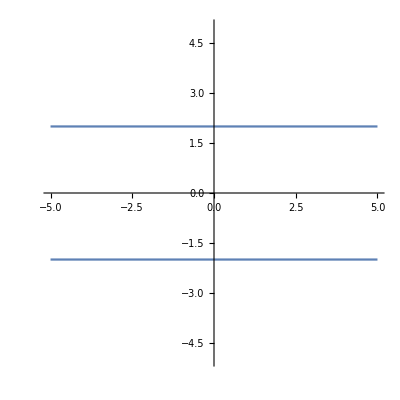

```mathematica
Show[Plot[left[x], {x, -5, 5}, PlotRange->{-5,5}, AspectRatio->1],
Plot[top[x], {x, -5, 5}], Plot[right[x], {x, -5, 5}], Plot[down[x], {x, -5, 5}],
ListPlot[rightDownPoints], ListPlot[rightHighPoints], ListPlot[leftDownPoints], ListPlot[leftHighPoints]]
```

XOR

## Implémentation des tests

Test du Perceptron Linéaire simple

## Cas de test : Simple Linéairement Séparable

### Classification

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest]
```

```mathematica
model = createLinearModel[2,1];
```

NET::netexcptn: A .NET exception occurred: System.EntryPointNotFoundException: Impossible de trouver le point d'entrée 'createLinearModel' dans la DLL 'D:\git\projet_annuel_ibd3a\C++_lib\Dll-Machine-Learning\x64\Debug\Dll-Machine-Learning.dll'.
   à Wolfram.NETLink.DynamicDLLNamespace.DLLWrapper38.createLinearModel(Int32 , Int32 ).

```mathematica
X=Flatten[{positivePointsL, negativePointsL}];
Y = {1,1,1, -1,-1,-1};
```

```mathematica
Xtest = {X[[1]], X[[2]]};
Ytest = {Y[[1]]};
```

```mathematica
linearFitClassificationRosenblatt[model, X, 12 Y, 1, 1000, 0.1];
```

NET::methodargs: Improper arguments supplied for method named linearFitClassificationRosenblatt.

```mathematica
linearClassify[model, Xtest, 2, Ytest, 1];
```

NET::methodargs: Improper arguments supplied for method named linearClassify.

```mathematica
Xtest2 = Partition[Flatten[Table[{i,j},{i, -5, 5, 0.2}, {j, -5, 5, 0.2}]], 2];
```

```mathematica
positive = Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== 1&];
negative =Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== -1&];
```

NET::methodargs: Improper arguments supplied for method named linearClassify.

General::stop: Further output of NET::methodargs will be suppressed during this calculation.

NET::methodargs: Improper arguments supplied for method named linearClassify.

General::stop: Further output of NET::methodargs will be suppressed during this calculation.

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],ListPlot[positive, PlotStyle->Red], ListPlot[negative, PlotStyle->Blue], ListPlot[negativePointsL, PlotStyle->Blue, PlotStyle->Thick],
ListPlot[positivePointsL, PlotStyle->Red, PlotStyle->Thick]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest];
```

```mathematica
managedTab = NETNew["int[]", 5]
LoadNETType["System.Runtime.InteropServices.Marshal"]
Marshal`Copy[funct, managedTab, 0, 5]
managedTab@GetValue[2]
```

«NETObject[System.Int32[]]»

NETType[System.Runtime.InteropServices.Marshal,68]

NET::methodargs: Improper arguments supplied for method named Copy.

$Failed

0

```mathematica
copyFromNetArray[array_] := Table[array@GetValue[i], {i, 0, array@Length-1}]
```

```mathematica
NETObjectToExpression[managedTab]
```

{0,0,0,0,0}

### Régression

## Cas de test : Simple Non-Linéairement Séparable

### Classification

### Régression

## Cas de test : Cross

## Cas de test : XOR

Test du Perceptron Multi Couches

## Cas de test : Simple Linéairement Séparable

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest]
```

```mathematica
model = createLinearModel[2,1];
```

NET::netexcptn: A .NET exception occurred: System.EntryPointNotFoundException: Impossible de trouver le point d'entrée 'createLinearModel' dans la DLL 'D:\git\projet_annuel_ibd3a\C++_lib\Dll-Machine-Learning\x64\Debug\Dll-Machine-Learning.dll'.
   à Wolfram.NETLink.DynamicDLLNamespace.DLLWrapper38.createLinearModel(Int32 , Int32 ).

```mathematica
X=Flatten[{positivePointsL, negativePointsL}];
Y = {1,1,1, -1,-1,-1};
```

```mathematica
Xtest = {X[[1]], X[[2]]};
Ytest = {Y[[1]]};
```

```mathematica
linearFitClassificationRosenblatt[model, X, 12 Y, 1, 1000, 0.1];
```

NET::methodargs: Improper arguments supplied for method named linearFitClassificationRosenblatt.

```mathematica
linearClassify[model, Xtest, 2, Ytest, 1];
```

NET::methodargs: Improper arguments supplied for method named linearClassify.

```mathematica
Xtest2 = Partition[Flatten[Table[{i,j},{i, -5, 5, 0.2}, {j, -5, 5, 0.2}]], 2];
```

```mathematica
positive = Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== 1&];
negative =Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== -1&];
```

NET::methodargs: Improper arguments supplied for method named linearClassify.

General::stop: Further output of NET::methodargs will be suppressed during this calculation.

NET::methodargs: Improper arguments supplied for method named linearClassify.

General::stop: Further output of NET::methodargs will be suppressed during this calculation.

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],ListPlot[positive, PlotStyle->Red], ListPlot[negative, PlotStyle->Blue], ListPlot[negativePointsL, PlotStyle->Blue, PlotStyle->Thick],
ListPlot[positivePointsL, PlotStyle->Red, PlotStyle->Thick]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest];
```

```mathematica
managedTab = NETNew["int[]", 5]
LoadNETType["System.Runtime.InteropServices.Marshal"]
Marshal`Copy[funct, managedTab, 0, 5]
managedTab@GetValue[2]
```

«NETObject[System.Int32[]]»

NETType[System.Runtime.InteropServices.Marshal,68]

NET::methodargs: Improper arguments supplied for method named Copy.

$Failed

0

```mathematica
copyFromNetArray[array_] := Table[array@GetValue[i], {i, 0, array@Length-1}]
```

```mathematica
NETObjectToExpression[managedTab]
```

{0,0,0,0,0}

## Cas de test : Simple Non-Linéairement Séparable

## Cas de test : Cross

## Cas de test : XOR

Test du RBF

## Cas de test : Simple Linéairement Séparable

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest]
```

```mathematica
model = createLinearModel[2,1];
```

NET::netexcptn: A .NET exception occurred: System.EntryPointNotFoundException: Impossible de trouver le point d'entrée 'createLinearModel' dans la DLL 'D:\git\projet_annuel_ibd3a\C++_lib\Dll-Machine-Learning\x64\Debug\Dll-Machine-Learning.dll'.
   à Wolfram.NETLink.DynamicDLLNamespace.DLLWrapper38.createLinearModel(Int32 , Int32 ).

```mathematica
X=Flatten[{positivePointsL, negativePointsL}];
Y = {1,1,1, -1,-1,-1};
```

```mathematica
Xtest = {X[[1]], X[[2]]};
Ytest = {Y[[1]]};
```

```mathematica
linearFitClassificationRosenblatt[model, X, 12 Y, 1, 1000, 0.1];
```

NET::methodargs: Improper arguments supplied for method named linearFitClassificationRosenblatt.

```mathematica
linearClassify[model, Xtest, 2, Ytest, 1];
```

NET::methodargs: Improper arguments supplied for method named linearClassify.

```mathematica
Xtest2 = Partition[Flatten[Table[{i,j},{i, -5, 5, 0.2}, {j, -5, 5, 0.2}]], 2];
```

```mathematica
positive = Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== 1&];
negative =Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== -1&];
```

NET::methodargs: Improper arguments supplied for method named linearClassify.

General::stop: Further output of NET::methodargs will be suppressed during this calculation.

NET::methodargs: Improper arguments supplied for method named linearClassify.

General::stop: Further output of NET::methodargs will be suppressed during this calculation.

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],ListPlot[positive, PlotStyle->Red], ListPlot[negative, PlotStyle->Blue], ListPlot[negativePointsL, PlotStyle->Blue, PlotStyle->Thick],
ListPlot[positivePointsL, PlotStyle->Red, PlotStyle->Thick]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest];
```

```mathematica
managedTab = NETNew["int[]", 5]
LoadNETType["System.Runtime.InteropServices.Marshal"]
Marshal`Copy[funct, managedTab, 0, 5]
managedTab@GetValue[2]
```

«NETObject[System.Int32[]]»

NETType[System.Runtime.InteropServices.Marshal,68]

NET::methodargs: Improper arguments supplied for method named Copy.

$Failed

0

```mathematica
copyFromNetArray[array_] := Table[array@GetValue[i], {i, 0, array@Length-1}]
```

```mathematica
NETObjectToExpression[managedTab]
```

{0,0,0,0,0}

## Cas de test : Simple Non-Linéairement Séparable

## Cas de test : Cross

## Cas de test : XOR